## init: collection of functions used

```mathematica
GenerateROCsmart[xadjA_,adjA_:adjA,focusXcoord_:False]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
If[Dimensions@xadjA≠Dimensions@adjA,
Print["GenerateROCsmart error: Dimensions of input matrices do not match"];Abort[]];
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
(* If[xmax-xmin<10^-9,Abort[]]; *)
If[xmax-xmin>10^-9,
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=GenerateROCrecursive[xdata,{0,0},xmax,{1,1},xmin,xROCpoints,0.04,1,focusXcoord];
$RecursionLimit=oldRL;
];
Return@Sort@xROCpoints
];
GenerateROCrecursive[xdata_,left_,xmax_,right_,xmin_,xROCpoints_,minDist2D_,recursionDepth_Integer,focusXcoord_:False]:=Module[{xx,xP,xTP,xN,xFP,xROCpointsLocal,middle},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
xx=N@((xmin+xmax)/2);
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];
(*Print["New ROC point: "<>ToString@middle<>", xx="<>ToString@InputForm@xx<>", left="<>ToString@left<>", xmin="<>ToString@InputForm@xmin<>", right="<>ToString@right<>", xmax="<>ToString@InputForm@xmax];
Pause[0.1];*)
If[(Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1)&&(recursionDepth<20),
If[Norm[middle-left]>minDist2D,
If[(focusXcoord==False)||((First@left≤focusXcoord)&&(focusXcoord≤First@middle)),
xROCpointsLocal=GenerateROCrecursive[xdata,left,xmax,middle,xx,xROCpointsLocal,minDist2D,recursionDepth+1,focusXcoord]]];
If[Norm[right-middle]>minDist2D,
If[(focusXcoord==False)||((First@middle≤focusXcoord)&&(focusXcoord≤First@right)),
xROCpointsLocal=GenerateROCrecursive[xdata,middle,xx,right,xmin,xROCpointsLocal,minDist2D,recursionDepth+1,focusXcoord]]];
];
xROCpointsLocal
];
GenerateROCsmartVector[xoriginal_,xrec_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0.,0},{1,1}};
xdata=Transpose@{xoriginal,xrec};
xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
(* If[xmax-xmin<10^-9,Abort[]]; *)
If[xmax-xmin>10^-9,
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=GenerateROCrecursive[xdata,{0.,0},xmax,{1,1},xmin,xROCpoints,0.04];
$RecursionLimit=oldRL;
];
Sort@xROCpoints
];

ReduceForInterpolation[xdataIn_]:=Module[{ii,xdata,xdata2},
xdata=N@xdataIn;
xdata2={};
For[ii=1,ii≤Length@xdata,ii++,
If[Length@Cases[xdata2,{xdata⟦ii,1⟧,_}]==0,
AppendTo[xdata2,xdata⟦ii⟧]
]];
xdata2
];
TPat10FP[xadjA_,trueadjA_,xcoord_:0.1]:=Interpolation[ReduceForInterpolation@N@GenerateROCsmart[xadjA,trueadjA,xcoord],InterpolationOrder->1][xcoord];
```

```mathematica
CleanUpROCs[roc_List]:=Module[{xrocN,xValues},
xrocN=N[roc,3];
xValues=Union[xrocN⟦All,1⟧];
Return[{#,Last@First@Cases[xrocN,{#,_}]}&/@xValues];
];
```

```mathematica
TellMeWhatHappened[parslist_]:=TellMeWhatHappened[parslist,-1];
TellMeWhatHappened[parslist_,maxit_]:=Module[{ii,jj,constantlist,length,therewas1before},
If[Length@Union[Length/@parslist]≠1,Abort[]];
If[Length@Dimensions@parslist>1,
length=Length@First@parslist;
constantlist=Table[If[Length@Union[parslist⟦All,ii⟧]==1,True,False],{ii,length}];

Print["constant parameters:"];
Print[Second@Transpose@Cases[Transpose[{constantlist,First@parslist}],{True,_}]];
Print["variable parameters:"];
For[ii=1,ii≤Length@parslist,ii++,
Print["#",ii,": ",Second@Transpose@Cases[Transpose[{constantlist,parslist⟦ii⟧}],{False,_}]];
If[(maxit>0)&&(ii≥maxit),
Print["(remaining "<>ToString[Length[parslist]-ii]<>" iterations hidden.)"];
Break[];
];
];
,
Print["parameters: ",parslist];
];
];
```

```mathematica
NTP[adjAD_,trueadjA_]:=Length@Cases[Transpose[N@Flatten@RemoveDiagonal@Normal@#&/@{adjAD,trueadjA}],{1.,1.}];
NFP[adjAD_,trueadjA_]:=Length@Cases[Transpose[N@Flatten@RemoveDiagonal@Normal@#&/@{adjAD,trueadjA}],{1.,0.}];
PPCpoint[adjAD_,trueadjA_,numberOfLinks_]:=(NTP[adjAD,trueadjA]-NFP[adjAD,trueadjA])/numberOfLinks;
GeneratePPC[adjA_,trueadjA_,stepsize_:10]:=Module[{d=Length@adjA,adjAD},
Return@Table[{n,adjAD=ThresholdedNumberA[adjA,n];N@PPCpoint[adjAD,trueadjA,n]},{n,1,d*(d-1),stepsize}]
];
```

## examine reconstruction quality for a given conditioning level

#### set up parameters

```mathematica
SetDirectory["~/Desktop/Doktorarbeit/Causality/challenge"];
adjAdir = "topologies";
networkSizes={50,100,500};
topoIndices=Range[0.1,0.6,0.1];
iNet=1;
```

```mathematica
Tuples[{networkSizes,topoIndices}]
```

{{50,0.1},{50,0.2},{50,0.3},{50,0.4},{50,0.5},{50,0.6},{100,0.1},{100,0.2},{100,0.3},{100,0.4},{100,0.5},{100,0.6},{500,0.1},{500,0.2},{500,0.3},{500,0.4},{500,0.5},{500,0.6}}

#### load ground truth matrices

```mathematica
trueadjAs=trueposlists={};
Do[
{s,cc}=topology;
filename=adjAdir<>"/topology_iNet"<>ToString[iNet]<>"_Size"<>ToString[s]<>"_CC0"<>ToString[Round[10 cc]]<>".yaml";
(* Print@filename; *)
If[FileExistsQ[filename],
Print["importing ",filename," ..."];
AppendTo[trueadjAs,{s,cc,First[ximport=ImportNetworkFromYAML[filename]]}];
AppendTo[trueposlists,{s,cc,Second@ximport}];
,
Print["YAML matrix input file ",filename," not found!"];
Abort[];
];
,{topology,Tuples[{networkSizes,topoIndices}]}];
Print["done."];
Clear[s,cc,filename,ximport];
```

#### evaluate quality of reconstructions

```mathematica
ROCs=TP10percents={};
recFiles=Sort@FileNames["reconstructions/adjA*.mx"];
parsFiles=Sort@FileNames["reconstructions/pars*.mx"];

Do[
{recFileName,parsFileName}=fff;
pars=Get[parsFileName];
s=Symbol["size"]/.pars;
(* the following assumes a fluoro. file name format ending in ..._CC01.txt *)
cc=0.1*ToExpression[StringTake[Symbol["inputfile"]/.pars,{-5}]];
Print["analyzing ",recFileName," (s = ",s,", cc = ",cc,") ..."];

trueadjA=Last@First@Cases[trueadjAs,{s,cc,__}];

xadjA=Get[recFileName];
(* take lowest global bin, if more than one is available *)
If[Length@Dimensions@xadjA>2,xadjA=xadjA⟦All,All,1⟧];

AppendTo[ROCs,{s,cc,GenerateROCsmart[xadjA,trueadjA]}];
AppendTo[TP10percents,{s,cc,xtp=TPat10FP[xadjA,trueadjA]}];
Print["-> found TP@10%FP performance of ",xtp];

,{fff,Transpose@{recFiles,parsFiles}}];
Clear[pars,s,cc,trueadjA,xadjA,xtp];
TP10percents
```

## examine reconstruction quality when scanning conditioning levels

#### set up parameters

```mathematica
SetDirectory["~/Desktop/Doktorarbeit/Causality/challenge"];
adjAdir = "topologies";
networkSizes={50,100,500};
topoIndices=Range[0.1,0.6,0.1];
iNet=1;
```

#### load ground truth matrices

```mathematica
trueadjAs=trueposlists={};
Do[
{s,cc}=topology;
filename=adjAdir<>"/topology_iNet"<>ToString[iNet]<>"_Size"<>ToString[s]<>"_CC0"<>ToString[Round[10 cc]]<>".yaml";
(* Print@filename; *)
If[FileExistsQ[filename],
Print["importing ",filename," ..."];
AppendTo[trueadjAs,{s,cc,First[ximport=ImportNetworkFromYAML[filename]]}];
AppendTo[trueposlists,{s,cc,Second@ximport}];
,
Print["YAML matrix input file ",filename," not found!"];
Abort[];
];
,{topology,Tuples[{networkSizes,topoIndices}]}];
Print["done."];
Clear[s,cc,filename,ximport];
```

#### evaluate quality of reconstructions (if all files present)

```mathematica
TP10percents={};
recFiles=Sort@FileNames["reconstructions/adjA*.mx"];
parsFiles=Sort@FileNames["reconstructions/pars*.mx"];

Do[
{recFileName,parsFileName}=fff;
pars=Get[parsFileName];
s=Symbol["size"]/.pars;
(* the following assumes a fluoro. file name format ending in ..._CC01.txt *)
cc=0.1*ToExpression[StringTake[Symbol["inputfile"]/.pars,{-5}]];
cond=N[Symbol["GlobalConditioningLevel"]/.pars];
Print["analyzing ",recFileName," (s = ",s,", cc = ",cc,", cond = ",cond,") ..."];

trueadjA=Last@First@Cases[trueadjAs,{s,cc,__}];

xadjA=Get[recFileName];
(* take lowest global bin, if more than one is available *)
If[Length@Dimensions@xadjA>2,xadjA=xadjA⟦All,All,1⟧];

(*AppendTo[ROCs,{s,cc,cond,GenerateROCsmart[xadjA,trueadjA]}];*)
AppendTo[TP10percents,{s,cc,cond,xtp=TPat10FP[xadjA,trueadjA]}];
Print["-> found TP@10%FP performance of ",xtp];

,{fff,Transpose@{recFiles,parsFiles}}];
Clear[pars,s,cc,cond,trueadjA,xadjA,xtp];
```

#### evaluate quality of reconstructions (if not all files present)

```mathematica
TP10percents={};
recFiles=Sort@FileNames["reconstructions/adjA*.mx"];
(*parsFiles=Sort@FileNames["reconstructions/pars*.mx"];*)

Do[
(*{recFileName,parsFileName}=fff;*)
fileIndex=ToExpression@StringTrim[recFileName,Except[DigitCharacter]...];
pars=Get["reconstructions/pars_iteration"<>ToString[fileIndex]<>".mx"];
s=Symbol["size"]/.pars;
(* the following assumes a fluoro. file name format ending in ..._CC01.txt *)
cc=0.1*ToExpression[StringTake[Symbol["inputfile"]/.pars,{-5}]];
cond=N[Symbol["GlobalConditioningLevel"]/.pars];
Print["analyzing ",recFileName," (s = ",s,", cc = ",cc,", cond = ",cond,") ..."];

trueadjA=Last@First@Cases[trueadjAs,{s,cc,__}];

xadjA=Get[recFileName];
(* take lowest global bin, if more than one is available *)
If[Length@Dimensions@xadjA>2,xadjA=xadjA⟦All,All,1⟧];

(*AppendTo[ROCs,{s,cc,cond,GenerateROCsmart[xadjA,trueadjA]}];*)
AppendTo[TP10percents,{s,cc,cond,xtp=TPat10FP[xadjA,trueadjA]}];
Print["-> found TP@10%FP performance of ",xtp];

,{recFileName,recFiles}];
Clear[fileIndex,pars,s,cc,cond,trueadjA,xadjA,xtp];
```

```mathematica
TP10percents>>"reconstructions/TP10percents.mx";
```

```mathematica
TP10percents=<<"reconstructions/TP10percents.mx";
```

```mathematica
tempSize=100;
tempCC=0.1;
ListPlot[Cases[TP10percents,{tempSize,tempCC,__}]⟦All,3;;⟧,PlotRange->All,Joined->True,PlotMarkers->Automatic,FrameLabel->{"cond. level","TP@10%FP"}]
```

```mathematica
tempSize=100;
GraphicsRow[ListPlot[Sort@Cases[TP10percents,{tempSize,#,__}]⟦All,3;;⟧,PlotRange->{0,1},Joined->True,PlotMarkers->Automatic,FrameLabel->{"cond. level","TP@10%FP"}]&/@topoIndices,ImageSize->350*Length[topoIndices]]
```

```mathematica
GraphicsGrid[Table[ListPlot[Sort@Cases[TP10percents,{tempSize,topo,__}]⟦All,3;;⟧,PlotRange->{0,1},Joined->True,PlotMarkers->Automatic,FrameLabel->{"cond. level","TP@10%FP"},PlotLabel->"N = "<>ToString@tempSize<>", CC = "<>ToString@topo],{tempSize,networkSizes},{topo,topoIndices}],ImageSize->350*Length[topoIndices]]
```

```mathematica
condLevels=Union@TP10percents⟦All,3⟧
```

{0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625}

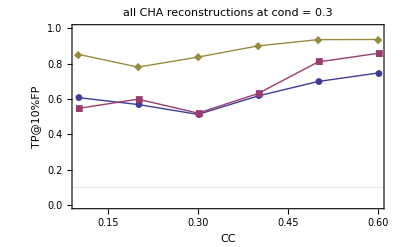

```mathematica
cond=0.3;
xlines=Table[Flatten[Cases[TP10percents,{tempSize,topo,cond,_}]⟦All,{2,-1}⟧,1],{tempSize,networkSizes},{topo,topoIndices}];
ListPlot[xlines,PlotRange->{0,1},Joined->True,PlotMarkers->Automatic,FrameLabel->{"CC","TP@10%FP"},GridLines->{{},{0.1}},PlotLabel->"all CHA reconstructions at cond = "<>ToString@cond]
```

### For a specific cond. level, select reconstructions and export ROC curves

```mathematica
xCondLevel=cond
```

0.3

```mathematica
ROCsList={};
recFiles=Sort@FileNames["reconstructions/adjA*.mx"];

Do[
fileIndex=ToExpression@StringTrim[recFileName,Except[DigitCharacter]...];
pars=Get["reconstructions/pars_iteration"<>ToString[fileIndex]<>".mx"];
s=Symbol["size"]/.pars;
(* the following assumes a fluoro. file name format ending in ..._CC01.txt *)
cc=0.1*ToExpression[StringTake[Symbol["inputfile"]/.pars,{-5}]];
cond=N[Symbol["GlobalConditioningLevel"]/.pars];

If[cond==xCondLevel,
Print["analyzing ",recFileName," (s = ",s,", cc = ",cc,", cond = ",cond,") ..."];

trueadjA=Last@First@Cases[trueadjAs,{s,cc,__}];

xadjA=Get[recFileName];
(* take lowest global bin, if more than one is available *)
If[Length@Dimensions@xadjA>2,xadjA=xadjA⟦All,All,1⟧];

AppendTo[ROCsList,{s,cc,cond,xroc=CleanUpROCs@GenerateROCsmart[xadjA,trueadjA]}];
exportName="roc_curves/roc_iNet1_Size"<>ToString[s]<>"_CC0"<>ToString[Round[cc*10]]<>".csv";
Export[exportName,xroc];
];

,{recFileName,recFiles}];
Clear[fileIndex,pars,s,cc,cond,trueadjA,xadjA,xroc,exportName];
```